# Differential Equations

## Computing and Modeling, Fourth Edition

C. Henry Edwards and David E. Penney

## 1 First-Order Differential Equations

## 1.1 Differential Equations and Mathematical Models

```mathematica
D[Tan[x],x]
```

Sec[x]^2

### 17.

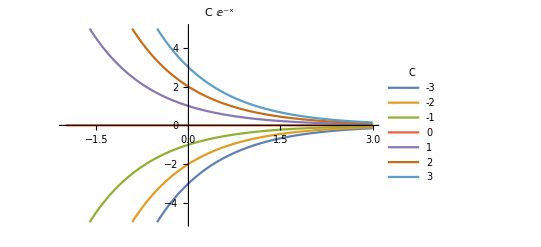

```mathematica
f[x_,C_]:=C ⅇ^-x;
Plot[Evaluate@Table[f[x,C],{C,-3,3,1}],{x,-2,3},PlotLegends->LineLegend[Table[C,{C,-3,3,1}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-5,5}]
Clear[f];
```

### 18.

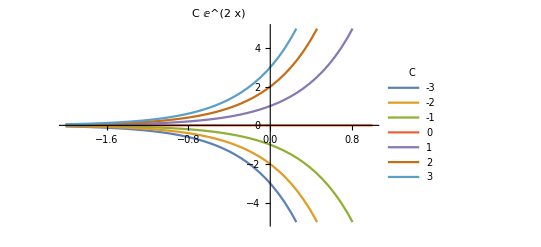

```mathematica
f[x_,C_]:=C ⅇ^(2x);
Plot[Evaluate@Table[f[x,C],{C,-3,3,1}],{x,-2,1},PlotLegends->LineLegend[Table[C,{C,-3,3,1}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-5,5}]
Clear[f];
```

### 19.

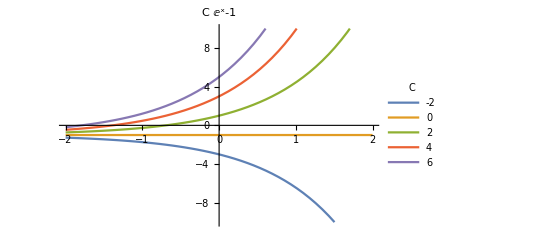

```mathematica
f[x_,C_]:=C ⅇ^x-1;
Plot[Evaluate@Table[f[x,C],{C,-2,6,2}],{x,-2,2},PlotLegends->LineLegend[Table[C,{C,-2,6,2}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-10,10}]
Clear[f];
```

### 20.

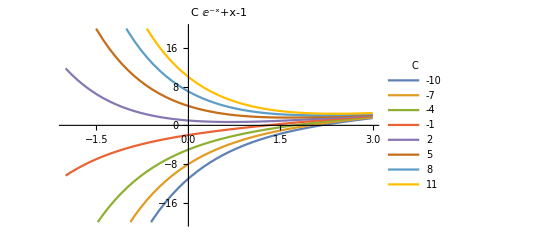

```mathematica
f[x_,C_]:=C ⅇ^-x+x-1;
Plot[Evaluate@Table[f[x,C],{C,-10,11,3}],{x,-2,3},PlotLegends->LineLegend[Table[C,{C,-10,11,3}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-20,20}]
Clear[f];
```

### 21.

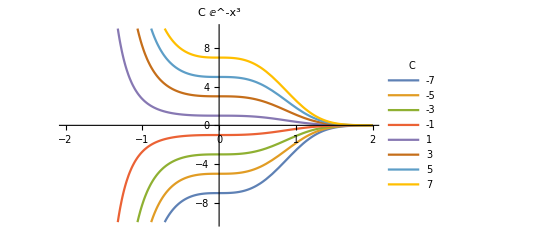

```mathematica
f[x_,C_]:=C ⅇ^(-x^3);
Plot[Evaluate@Table[f[x,C],{C,-7,7,2}],{x,-2,2},PlotLegends->LineLegend[Table[C,{C,-7,7,2}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-10,10}]
Clear[f];
```

### 22.

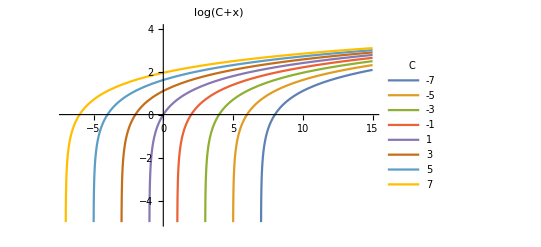

```mathematica
f[x_,C_]:=Log[x+C];
Plot[Evaluate@Table[f[x,C],{C,-7,7,2}],{x,-10,15},PlotLegends->LineLegend[Table[C,{C,-7,7,2}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-5,4}]
Clear[f];
```

### 23.

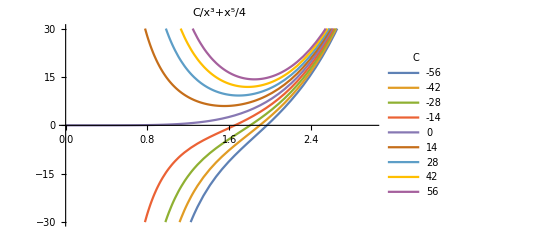

```mathematica
f[x_,C_]:=1/4 x^5+C x^-3;
Plot[Evaluate@Table[f[x,C],{C,-56,56,14}],{x,0,3},PlotLegends->LineLegend[Table[C,{C,-56,56,14}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-30,30}]
Clear[f];
```

### 24.

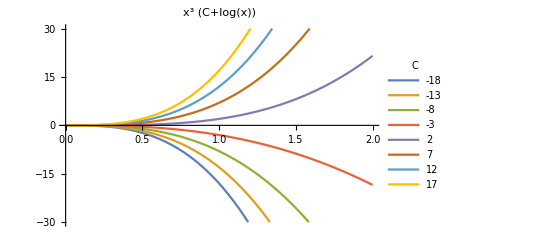

```mathematica
f[x_,C_]:=x^3(C+Log[x]);
Plot[Evaluate@Table[f[x,C],{C,-18,17,5}],{x,0,2},PlotLegends->LineLegend[Table[C,{C,-18,17,5}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-30,30}]
Clear[f];
```

### 25.

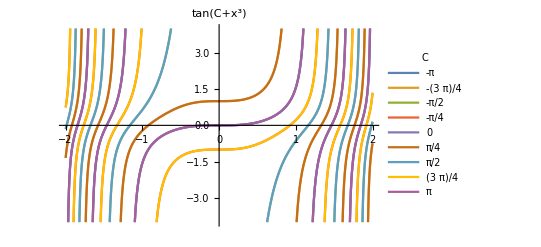

```mathematica
f[x_,C_]:=Tan[x^3+C];
Plot[Evaluate@Table[f[x,C],{C,-π,π,π/4}],{x,-2,2},PlotLegends->LineLegend[Table[C,{C,-π,π,π/4}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-4,4}]
Clear[f];
```

### 26.

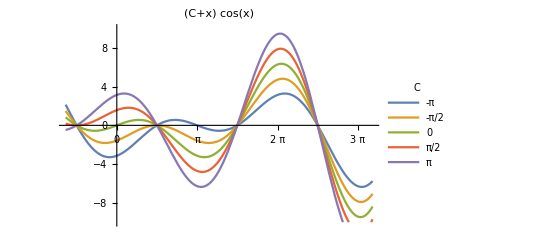

```mathematica
f[x_,C_]:=(x+C)Cos[x];
Plot[Evaluate@Table[f[x,C],{C,-π,π,π/2}],{x,-2,10},PlotLegends->LineLegend[Table[C,{C,-π,π,π/2}],LegendLabel->C],PlotLabel->f[x,C],PlotRange->{-10,10},Ticks->{Range[-π,3π,π/4],Automatic}]
Clear[f];
```

### 30.

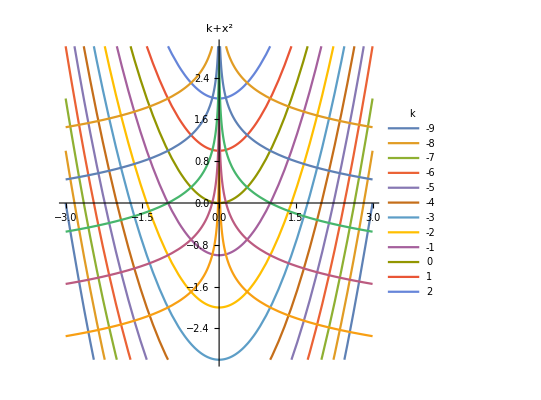

```mathematica
f[x_,k_]:=x^2+k;
g[x_,k_]:=-1/2 Log[Abs[x]]+k;
Plot[{Evaluate@Table[f[x,k],{k,-9,2,1}],Evaluate@Table[g[x,k],{k,-2,2,1}]},{x,-3,3},PlotLegends->LineLegend[Table[k,{k,-9,2,1}],LegendLabel->k],PlotLabel->f[x,k],PlotRange->{-3,3},AspectRatio->1]
Clear[f];
Clear[g];
```

### 44.

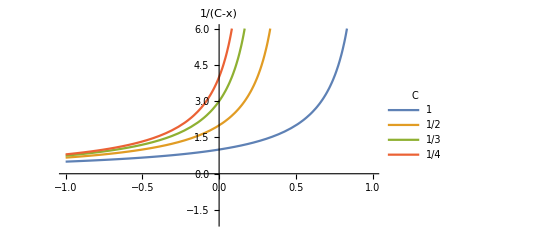

```mathematica
f[t_,k_,C_]:=1/(C-k t);
Plot[Evaluate@Table[f[x,1,1/C],{C,1,4,1}],{x,-1,1},PlotLegends->LineLegend[Table[1/C,{C,1,4,1}],LegendLabel->C],PlotLabel->f[x,1,C],RegionFunction->(#2≥0&),PlotRange->{-2,6}]
Clear[f];
```

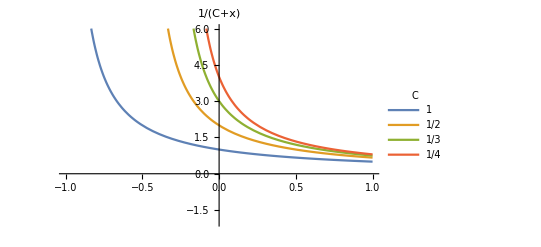

```mathematica
f[t_,k_,C_]:=1/(C-k t);
Plot[Evaluate@Table[f[x,-1,1/C],{C,1,4,1}],{x,-1,1},PlotLegends->LineLegend[Table[1/C,{C,1,4,1}],LegendLabel->C],PlotLabel->f[x,-1,C],RegionFunction->(#2≥0&),PlotRange->{-2,6}]
Clear[f];
```